## 1)

### (a)

```mathematica
ϕ0[x_]=ⅇ^(-1/(2ν)∫_0^x u0[y]ⅆy);
ϕ[x_,t_]=1/(√(4π ν t))∫_(-∞)^∞ ϕ0[ξ] ⅇ^((-(x-ξ)^2)/(4ν t))ⅆξ;
u[x_,t_]=-2ν D[Log[ϕ[x,t]], x]
```

-(2 ν ∫_(-∞)^∞ -(ⅇ^(-(x-ξ)^2/(4 t ν)-(∫_0^ξ u0[y]ⅆy)/(2 ν)) (x-ξ))/(2 t ν)ⅆξ)/(∫_(-∞)^∞ ⅇ^(-(x-ξ)^2/(4 t ν)-(∫_0^ξ u0[y]ⅆy)/(2 ν))ⅆξ)

```mathematica
D[ϕ[x,t], x]//FullSimplify
```

(∫_(-∞)^∞ (ⅇ^(-((x-ξ)^2+2 t ∫_0^ξ u0[y]ⅆy)/(4 t ν)) (-x+ξ))/(2 t ν)ⅆξ)/(2 √π √(t ν))

```mathematica
ϕ[x,t]//FullSimplify
```

(∫_(-∞)^∞ ⅇ^(-((x-ξ)^2+2 t ∫_0^ξ u0[y]ⅆy)/(4 t ν))ⅆξ)/(2 √π √(t ν))

### (b)

```mathematica
D[(-∫_0^ξ u0[y]ⅆy-(x-ξ)^2/(2t)), ξ]
D[(-∫_0^ξ u0[y]ⅆy-(x-ξ)^2/(2t)), ξ,ξ]
```

(x-ξ)/t-u0[ξ]

-1/t-u0'[ξ]

### (c)

```mathematica
DynamicModule[{u0,R},
u0[x_]=Piecewise[{{0, x<=0}, {1, x>0}}];
{R[ξ_,x_,t_]=Assuming[ξ∈Reals,-∫_0^ξ u0[y]ⅆy-(x-ξ)^2/(2t)],
Manipulate[Plot[R[ξ,x,t],{ξ,-5,5}],{{x,0},-10,10},{t,0.01,10}]}]
```

### (d)

```mathematica
DynamicModule[{u0,R},
u0[x_]=Piecewise[{{1, x<=0}, {0, x>0}}];
{R[ξ_,x_,t_]=Assuming[ξ∈Reals,-∫_0^ξ u0[y]ⅆy-(x-ξ)^2/(2t)],
Manipulate[Plot[R[ξ,x,t],{ξ,-5,5}],{{x,0},-10,10},{t,0.01,10}],
D[R[ξ,2,4], ξ],
Solve[D[R[ξ,3,4], ξ]==0,ξ]}]
```

## 2)

```mathematica
Assuming[x>0,1/π∫_0^π Cos[x Cos[θ]]ⅆθ]
```

BesselJ[0,x]

```mathematica
AsymptoticIntegrate[1/π Cos[x Cos[θ]],{θ,0,π},x->∞]
```

Cos[x]/(√π √x)+Sin[x]/(√π √x)

```mathematica
AsymptoticIntegrate[ⅇ^(ⅈ x Cos[θ]),{θ,0,π},x->∞]
```

(√π Cos[x])/(√x)+(√π Sin[x])/(√x)

```mathematica
Gamma[1/2]
```

√π

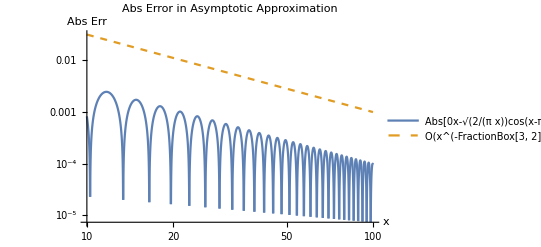

```mathematica
J0[x_]=√(2/(π x))Cos[x-π/4];
LogLogPlot[{Abs[J0[x]-BesselJ[0,x]],1/x^(3/2)},{x,10,100},
PlotLegends->{Abs[BesselJ[0,x]-"√(2/(π x))cos(x-π/4)"],"O(x^(-FractionBox[3, 2]))"},
PlotStyle->{Automatic,Dashed},
PlotLabel->"Abs Error in Asymptotic Approximation",
AxesLabel->{"x","Abs Err"}]
```